```mathematica
p[t_,w0_,w_]:=Conjugate[c[t,w0,w]]*c[t,w0,w];
Plot[p[t,2*Pi,2.2*Pi],{t,0,20}]
```

$Aborted

```mathematica
f1[x_,w_]=Sin[w*x]
```

Sin[w x]

```mathematica
c[t_,w0_,w_]:=-NIntegrate[f1[x,w]*Exp[I*w0*x],{x,0,t}]
```

```mathematica
p[t_,w0_,w_]:=Conjugate[c[t,w0,w]]*c[t,w0,w]
```

NIntegrate::nlim: x = t is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

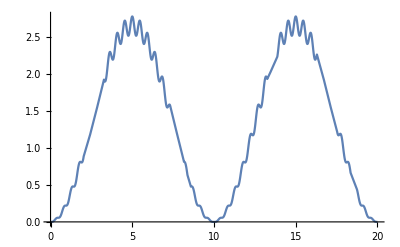

```mathematica
Plot[p[t,2*Pi,2.2*Pi],{t,0,20}]
```